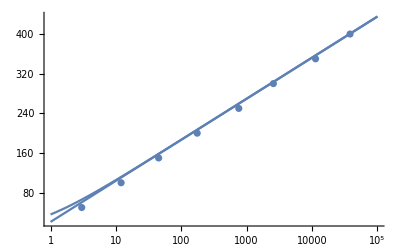

```mathematica
plotHn := LogLinearPlot[36 * HarmonicNumber[x], {x, 1, 100000}]
plotLogn := LogLinearPlot[21 + 36 * Log[x], {x, 1, 100000}]
counts := {{3,50}, {12,100}, {45,150}, {175, 200}, {757, 250}, {2559, 300}, {11293, 350}, {38079, 400}}
points:= ListLogLinearPlot[counts]
Show[{points, plotHn, plotLogn}, PlotRange->All]
```

```mathematica
N[21 + 36 * Log[200000]]
NSolve[21 + 36 * Log[D] == 450, D]
NSolve[21 + 36 * Log[D] == 500, D]
```

460.419

{{D→149742.}}

{{D→600523.}}

Determine good bounds on TF, trial factorization,

```mathematica
PrimePiApprox[n_] := N[n / Log[n]]
PrimesWithKBits[k_] := PrimePiApprox[2^(k+1)] - PrimePiApprox[2^k]
PrimesBetween[a_,b_] := Abs[PrimePiApprox[a] - PrimePiApprox[b]]
PropDivides[average_,count_] := N[Exp[count * Log[(1.0 - 1/average)]]]
```

```mathematica
k := 24
PP := PrimesWithKBits[k]
{PropDivides[ 2 ^ k, PP],PropDivides[ 2 ^ (k +0.5), PP],PropDivides[(2^k + 2^(k+1)) / 2, PP],PropDivides[ 2 ^ (k+1), PP]}
```

{0.944123,0.960158,0.962393,0.97166}

```mathematica
PropSplit[k_,n_]:= Module[
{first= 2^k, size=2^k / n, starts=Drop[Subdivide[2^k, 2^(k+1), n], -1]},
Times@@Map[#&, Map[PropDivides[# + size/2, PrimesBetween[#, #+size]]&, starts]]]
```

```mathematica
Times @@ Map[1.0 - 1/Prime[#]&,Range[PrimePi[2^k], PrimePi[2^(k+1)]]]
```

0.95834

```mathematica
Grid[Table[PropSplit[k,2^x], {k, 24, 32, 2}, {x,1,10}], Frame->All]
```

0.971343 | 0.971106 | 0.971044 | 0.971028 | 0.971024 | 0.971023 | 0.971023 | 0.971023 | 0.971023 | 0.971023
0.974313 | 0.974102 | 0.974046 | 0.974032 | 0.974029 | 0.974028 | 0.974027 | 0.974027 | 0.974027 | 0.974027
0.976726 | 0.976535 | 0.976484 | 0.976473 | 0.976469 | 0.976469 | 0.976468 | 0.976468 | 0.976468 | 0.976468
0.978701 | 0.978561 | 0.978514 | 0.978495 | 0.97849 | 0.978492 | 0.978491 | 0.97849 | 0.978491 | 0.97849
0.980358 | 0.980355 | 0.980243 | 0.980187 | 0.980104 | 0.980215 | 0.980194 | 0.980197 | 0.980197 | 0.980198

Product of (1 - 1/a) ^(chance a is prime), a = medium to big

```mathematica
N[Exp[Sum[Log[1 - 1/a] * 1/(Log[a] + -1.08366), {a, 2^k, 2^k}]]]
```

0.96819

```mathematica
UpToK =Table[{k,N[Product[1 - (1/Prime[i]),{i, 1, PrimePi[2^k]}]]}, {k,1,26}]
```

{{1,0.5},{2,0.333333},{3,0.228571},{4,0.191808},{5,0.152852},{6,0.131587},{7,0.113866},{8,0.100353},{9,0.0892559},{10,0.0806468},{11,0.0734532},{12,0.0673567},{13,0.06225},{14,0.0578045},{15,0.0539804},{16,0.0506133},{17,0.047637},{18,0.0449957},{19,0.042627},{20,0.0404985},{21,0.0385703},{22,0.0368177},{23,0.0352174},{24,0.0337502},{25,0.0324002},{26,0.0311542}}

```mathematica
PerK =Table[{k,N[Product[1 - (1/Prime[i]),{i, PrimePi[2^(k-1)]+1, PrimePi[2^k]}]]}, {k,1,30}]
```

{{1,0.5},{2,0.666667},{3,0.685714},{4,0.839161},{5,0.796901},{6,0.86088},{7,0.865329},{8,0.881325},{9,0.889417},{10,0.903546},{11,0.9108},{12,0.917003},{13,0.924183},{14,0.928587},{15,0.933844},{16,0.937622},{17,0.941196},{18,0.944555},{19,0.947357},{20,0.950065},{21,0.95239},{22,0.954559},{23,0.956535},{24,0.95834},{25,0.959998},{26,0.961545},{27,0.962966},{28,0.964286},{29,0.965519},{30,0.966667}}

```mathematica
Times@@Map[ #[[2]]&,PerK]
```

0.0270004

```mathematica
Error[IC_,JC_] = Table[1 - ( 1 -UpToK[[i]][[2]] * (i+IC)/(j+JC)) / PerK[[j]][[2]], {i,20,26}, {j, i+1, 30}]
TestE = Error[0, 5]
Grid[Round[TestE, 0.00001], Frame->All]
{Total[Join @@TestE],Count[Join @@ TestE, _?Negative], Count[Join @@TestE, _?Positive]}
```

{{1-1.04999 (1-(0.0404985 (20+IC))/(21+JC)),1-1.0476 (1-(0.0404985 (20+IC))/(22+JC)),1-1.04544 (1-(0.0404985 (20+IC))/(23+JC)),1-1.04347 (1-(0.0404985 (20+IC))/(24+JC)),1-1.04167 (1-(0.0404985 (20+IC))/(25+JC)),1-1.03999 (1-(0.0404985 (20+IC))/(26+JC)),1-1.03846 (1-(0.0404985 (20+IC))/(27+JC)),1-1.03704 (1-(0.0404985 (20+IC))/(28+JC)),1-1.03571 (1-(0.0404985 (20+IC))/(29+JC)),1-1.03448 (1-(0.0404985 (20+IC))/(30+JC))},{1-1.0476 (1-(0.0385703 (21+IC))/(22+JC)),1-1.04544 (1-(0.0385703 (21+IC))/(23+JC)),1-1.04347 (1-(0.0385703 (21+IC))/(24+JC)),1-1.04167 (1-(0.0385703 (21+IC))/(25+JC)),1-1.03999 (1-(0.0385703 (21+IC))/(26+JC)),1-1.03846 (1-(0.0385703 (21+IC))/(27+JC)),1-1.03704 (1-(0.0385703 (21+IC))/(28+JC)),1-1.03571 (1-(0.0385703 (21+IC))/(29+JC)),1-1.03448 (1-(0.0385703 (21+IC))/(30+JC))},{1-1.04544 (1-(0.0368177 (22+IC))/(23+JC)),1-1.04347 (1-(0.0368177 (22+IC))/(24+JC)),1-1.04167 (1-(0.0368177 (22+IC))/(25+JC)),1-1.03999 (1-(0.0368177 (22+IC))/(26+JC)),1-1.03846 (1-(0.0368177 (22+IC))/(27+JC)),1-1.03704 (1-(0.0368177 (22+IC))/(28+JC)),1-1.03571 (1-(0.0368177 (22+IC))/(29+JC)),1-1.03448 (1-(0.0368177 (22+IC))/(30+JC))},{1-1.04347 (1-(0.0352174 (23+IC))/(24+JC)),1-1.04167 (1-(0.0352174 (23+IC))/(25+JC)),1-1.03999 (1-(0.0352174 (23+IC))/(26+JC)),1-1.03846 (1-(0.0352174 (23+IC))/(27+JC)),1-1.03704 (1-(0.0352174 (23+IC))/(28+JC)),1-1.03571 (1-(0.0352174 (23+IC))/(29+JC)),1-1.03448 (1-(0.0352174 (23+IC))/(30+JC))},{1-1.04167 (1-(0.0337502 (24+IC))/(25+JC)),1-1.03999 (1-(0.0337502 (24+IC))/(26+JC)),1-1.03846 (1-(0.0337502 (24+IC))/(27+JC)),1-1.03704 (1-(0.0337502 (24+IC))/(28+JC)),1-1.03571 (1-(0.0337502 (24+IC))/(29+JC)),1-1.03448 (1-(0.0337502 (24+IC))/(30+JC))},{1-1.03999 (1-(0.0324002 (25+IC))/(26+JC)),1-1.03846 (1-(0.0324002 (25+IC))/(27+JC)),1-1.03704 (1-(0.0324002 (25+IC))/(28+JC)),1-1.03571 (1-(0.0324002 (25+IC))/(29+JC)),1-1.03448 (1-(0.0324002 (25+IC))/(30+JC))},{1-1.03846 (1-(0.0311542 (26+IC))/(27+JC)),1-1.03704 (1-(0.0311542 (26+IC))/(28+JC)),1-1.03571 (1-(0.0311542 (26+IC))/(29+JC)),1-1.03448 (1-(0.0311542 (26+IC))/(30+JC))}}

{{-0.0172798,-0.0161771,-0.0151982,-0.0143265,-0.0135447,-0.0128202,-0.0121737,-0.011583,-0.0110393,-0.0105429},{-0.0161768,-0.0151979,-0.0143262,-0.0135444,-0.0128199,-0.0121735,-0.0115827,-0.011039,-0.0105426},{-0.0151975,-0.0143258,-0.013544,-0.0128195,-0.0121731,-0.0115823,-0.0110387,-0.0105423},{-0.0143254,-0.0135436,-0.0128192,-0.0121727,-0.011582,-0.0110383,-0.010542},{-0.0135434,-0.012819,-0.0121725,-0.0115818,-0.0110382,-0.0105418},{-0.012819,-0.0121726,-0.0115819,-0.0110382,-0.0105418},{-0.0121724,-0.0115817,-0.011038,-0.0105417}}

-0.01728 | -0.01618 | -0.0152 | -0.01433 | -0.01354 | -0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054
-0.01618 | -0.0152 | -0.01433 | -0.01354 | -0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054 | 
-0.0152 | -0.01433 | -0.01354 | -0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054 |  | 
-0.01433 | -0.01354 | -0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054 |  |  | 
-0.01354 | -0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054 |  |  |  | 
-0.01282 | -0.01217 | -0.01158 | -0.01104 | -0.01054 |  |  |  |  | 
-0.01217 | -0.01158 | -0.01104 | -0.01054 |  |  |  |  |  |

{-0.614519,49,0}

```mathematica
Minimize[Abs[Total[Join@@Error[IC, JC]]], IJ, JC]
```

Minimize[Abs[IC+JC],IJ,JC]